```mathematica
(*

Decaying damping.

η = γ Log[t+1]

We verify errors against step size.

*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
pos[t_,γ_,q0_]:=1/2 q0 π (1+t)^(1/2-γ/2) (BesselJ[(1+γ)/2,1] BesselY[1/2 (-1+γ),1+t]-BesselJ[1/2 (-1+γ),1+t] BesselY[(1+γ)/2,1])
mom[t_,γ_,q0_]:=1/2 q0 π (1+t)^((1+γ)/2) (BesselJ[(1+γ)/2,1+t] BesselY[(1+γ)/2,1]-BesselJ[(1+γ)/2,1] BesselY[(1+γ)/2,1+t])
ham[q_,p_,t_,γ_]:=(1/2)(1+t)^-γ p^2 + (t+1)^γ q^2/2
```

```mathematica
Euler1[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

g=q;
p=p-h (t+1)^γ g;
q=q+h (t+1)^-γ p;
t=t+h;
numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{h,Max[data]}];

)

Euler2[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

t=t+h;
q=q+h (t+1)^-γ p;
g=q;
p=p-h (t+1)^γ g;

numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{h,Max[data]}];

)

Leapfrog1[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;
numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{h, Max[data]}];

)

Leapfrog2[q0_,γ_,maxT_,maxiter_]:=(

h=maxT/maxiter;
t=0;
q=q0;
p=0;

data={};
For[k=1,k≤maxiter,k++,

t=t+h/2;
q=q+(h/2)((t+1)^-γ) p;
g=q;
p=p-h (t+1)^γ g;
q=q+(h/2)(t+1)^-γ p;
t=t+h/2;
numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{h, Max[data]}];

)

Yoshida1[q0_,γ_,maxT_,maxiter_]:=(

ϵ=maxT/maxiter ;
t=0;
q=q0;
p=0;

data={};
κ=2^(1/3)//N;
For[k=1,k≤maxiter,k++,

a=1./(2.-κ);
h=a*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;


b=-κ/(2.-κ);
h=b*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;

a=1./(2.-κ);
h=a*ϵ;
g=q;
p=p-(h/2) (t+1)^γ g;
t=t+h;
q=q+(h/2)((t+1-h)^-γ+(t+1)^-γ) p;
g=q;
p=p-(h/2) (t+1)^γ g;

numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{ϵ, Max[data]}];

)

Yoshida2[q0_,γ_,maxT_,maxiter_]:=(

ϵ=maxT/maxiter ;
t=0;
q=q0;
p=0;

data={};
κ=2^(1/3)//N;
For[k=1,k≤maxiter,k++,

a=1./(2.-κ);
h=a*ϵ;
t=t+h/2;
q=q+(h/2)((t+1)^-γ) p;
g=q;
p=p-h (t+1)^γ g;
q=q+(h/2)(t+1)^-γ p;
t=t+h/2;

b=-κ/(2.-κ);
h=b*ϵ;
t=t+h/2;
q=q+(h/2)((t+1)^-γ) p;
g=q;
p=p-h (t+1)^γ g;
q=q+(h/2)(t+1)^-γ p;
t=t+h/2;

a=1./(2.-κ);
h=a*ϵ;
t=t+h/2;
q=q+(h/2)((t+1)^-γ) p;
g=q;
p=p-h (t+1)^γ g;
q=q+(h/2)(t+1)^-γ p;
t=t+h/2;

numham=ham[q,p,t,γ];

trueham=ham[pos[t,γ,q0],mom[t,γ,q0],t,γ];
AppendTo[data,Abs[trueham-numham]];

];

Return[{ϵ, Max[data]}];

)
```

```mathematica
maxiter=30000;
data1={};
data2={};
data3={};
For[k=maxiter, k≥50,k=k/1.5,
AppendTo[data1,Euler1[1.,3.,10.,k]];
AppendTo[data2,Leapfrog1[1.,3.,10.,k]];
AppendTo[data3,Yoshida1[1.,3.,10.,k]];
];
```

```mathematica
maxiter=30000;
data21={};
data22={};
data23={};
For[k=maxiter, k≥50,k=k/1.5,
AppendTo[data21,Euler2[1.,3.,10.,k]];
AppendTo[data22,Leapfrog2[1.,3.,10.,k]];
AppendTo[data23,Yoshida2[1.,3.,10.,k]];
];
```

```mathematica
line1={};
line2={};
line3={};
For[k=5000, k≥1000,k=k/1.5,
h=10./k;
AppendTo[line1,{h,0.8 h^1}];
AppendTo[line2,{h,0.2 h^2}];
AppendTo[line3,{h,0.2 h^4}];
];
```

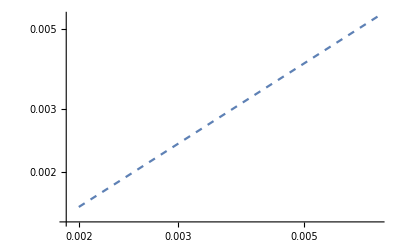

```mathematica
ListLogLogPlot[line1,Joined->True,PlotStyle->Dashed]
```

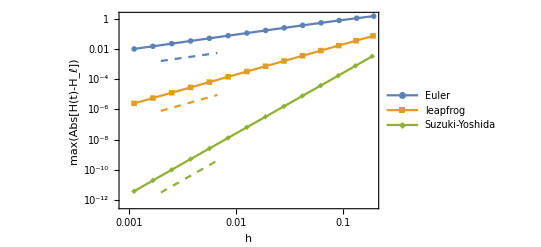

```mathematica
start=4;
g=Show[{ListLogLogPlot[{
data1[[start;;-1]],(*data21[[start;;-1]],*)
data2[[start;;-1]],(*data22[[start;;-1]],*)
data3[[start;;-1]]},(*data23[[start;;-1]]},*)
Joined->True,
Frame->True, 
FrameLabel->{Style[HoldForm[h],FontSize->14],Style[HoldForm[Max[Abs[H[t] - Subscript[H, ℓ]] ]],FontSize->14]},PlotLegends->Placed[{"Euler", "leapfrog", "Suzuki-Yoshida"},Top],
PlotMarkers->{Automatic,0.05}
],
ListLogLogPlot[line1,Joined->True,PlotStyle->{ColorData[97,"ColorList"][[1]],Dashed}],
ListLogLogPlot[line2,Joined->True,PlotStyle->{ColorData[97,"ColorList"][[2]],Dashed}],
ListLogLogPlot[line3,Joined->True,PlotStyle->{ColorData[97,"ColorList"][[3]],Dashed}]
}]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_order.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_order.pdf

```mathematica
data={};
For[k=30000, k≥50,k=k/1.5,AppendTo[data,k];];
data
```

{30000,20000.,13333.3,8888.89,5925.93,3950.62,2633.74,1755.83,1170.55,780.369,520.246,346.831,231.22,154.147,102.765,68.5097}

```mathematica
data3
```

{{0.0166556,1.93053×10^-7},{0.0199601,3.98232×10^-7},{0.0249004,9.64711×10^-7},{0.0330907,3.01002×10^-6},{0.0493097,0.0000148576},{0.0967118,0.000221034}}

```mathematica
dataEu=Euler1[1.,3.,50.,500];
dataLf=Leapfrog1[1.,3.,50.,500];
dataYo=Yoshida1[1.,3.,50.,500];
```

```mathematica
dataYo;
```

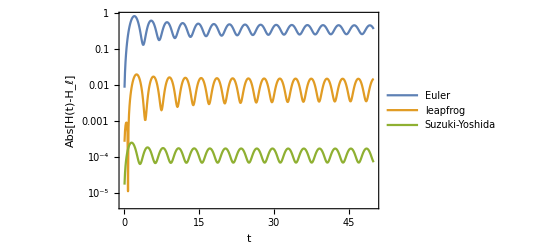

```mathematica
dataEu2 = Take[dataEu,{1,-1,1}];
dataLf2 = Take[dataLf,{1,-1,1}];
dataYo2=Take[dataYo,{1,-1,1}];
g=ListLogPlot[{
dataEu2[[All,{1,2}]],
dataLf2[[All,{1,2}]],
dataYo2[[All,{1,2}]]},
Joined->True,
Frame->True, 
FrameLabel->{Style[HoldForm[t],FontSize->14],Style[HoldForm[Abs[H[t] - Subscript[H, ℓ]] ],FontSize->14]},PlotLegends->Placed[{"Euler", "leapfrog", "Suzuki-Yoshida"},Top]]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_ham.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_dec_ham.pdf

```mathematica
Max[{1,2,10,3}]
```

10